```mathematica
Quit[]
```

```mathematica
NotebookDirectory[]
```

/Users/hayriyesundu/Documents/SUNDU/COLLABORATIONS/Bilimsel_Okullar/QCDSUMRULE_Online_16_20Jan2023/BMeson_HesapDosyasi/

```mathematica
SetDirectory[%]
```

/Users/hayriyesundu/Documents/SUNDU/COLLABORATIONS/Bilimsel_Okullar/QCDSUMRULE_Online_16_20Jan2023/BMeson_HesapDosyasi

```mathematica
mb=4.18;(*PDG*)
mq=2.16*10^(-3);(*PDG*)
qbq=(-0.241)^3;
mo=Sqrt[0.8];
alfsGGbolPi=0.012;(*(Subscript[α, s] G^2)/π*)
```

```mathematica
(*perturbative sonuc bilgileri*)
```

```mathematica
pert=<<StpmupnuIntu.out
```

(2 mb^6-3 mb^4 s+s^3)/(4 π^2 s^3)

```mathematica
pertElif=<<Stpmupnu.out
```

-(3 (-1+u) u)/(2 π^2)

```mathematica
rhopert[s_]:=(2 mb^6-3 mb^4 s+s^3)/(4 π^2 s^3)
```

```mathematica
L[s_,u_]:=-mb^2 u+s u-s u^2
```

```mathematica
rhopertElif[s_,u_]:=-(3 (-1+u) u)/(2 π^2)*UnitStep[L[s,u]]
```

```mathematica
(*Dim3 sonuc bilgileri*)
```

```mathematica
BorelDim3=<<BorelDim3Stpmupnu.out
```

(ⅇ^(-mb^2/M2) mq qbq)/M2

```mathematica
BPiDim3[M2_]:=(ⅇ^(-mb^2/M2) mq qbq)/M2
```

```mathematica
DerBorelDim3=<<TurevBorelDim3Stpmupnu.out
```

(ⅇ^(-mb^2/M2) (M2-mb^2) mq qbq)/M2

```mathematica
DerBPiDim3[M2_]:=(ⅇ^(-mb^2/M2) (M2-mb^2) mq qbq)/M2
```

```mathematica
(*Dim4 sonuc bilgileri*)
```

```mathematica
BorelDim4=<<BorelDim4Stpmupnu.out
```

(alfsGGbolPi ⅇ^(mb^2/(M2 (-1+u))) (M2 (-1+u)^2-mb^2 u))/(12 M2^2 (-1+u)^2)

```mathematica
BPiDim4[M2_,u_]:=(alfsGGbolPi ⅇ^(mb^2/(M2 (-1+u))) (M2 (-1+u)^2-mb^2 u))/(12 M2^2 (-1+u)^2);
```

```mathematica
DerBorelDim4=<<TurevBorelDim4Stpmupnu.out
```

(alfsGGbolPi ⅇ^(mb^2/(M2 (-1+u))) (M2^2 (-1+u)^3-mb^4 u-M2 mb^2 (-1+u^2)))/(12 M2^2 (-1+u)^3)

```mathematica
DerBPiDim4[M2_,u_]:=(alfsGGbolPi ⅇ^(mb^2/(M2 (-1+u))) (M2^2 (-1+u)^3-mb^4 u-M2 mb^2 (-1+u^2)))/(12 M2^2 (-1+u)^3)
```

```mathematica
(*Dim5 sonuc bilgileri*)
```

```mathematica
BorelDim5=<<BorelDim5Stpmupnu.out
```

-(ⅇ^(-mb^2/M2) mo^2 mq qbq)/(6 M2^2)-(ⅇ^(-mb^2/M2) mb^2 mo^2 mq qbq)/(6 M2^3)

```mathematica
BPiDim5[M2_]:=-(ⅇ^(-mb^2/M2) mo^2 mq qbq)/(6 M2^2)-(ⅇ^(-mb^2/M2) mb^2 mo^2 mq qbq)/(6 M2^3)
```

```mathematica
DerBorelDim5=<<TurevBorelDim5Stpmupnu.out
```

-(ⅇ^(-mb^2/M2) (2 M2^2+2 M2 mb^2-mb^4) mo^2 mq qbq)/(6 M2^3)

```mathematica
DerBPiDim5[M2_]:=-(ⅇ^(-mb^2/M2) (2 M2^2+2 M2 mb^2-mb^4) mo^2 mq qbq)/(6 M2^3)
```

```mathematica
(*KRD kısmı*)
```

```mathematica
Pert[M2_,s0_]:=NIntegrate[rhopert[s]*Exp[-s/M2],{s,(mb+mq)^2,s0}]
```

```mathematica
PertElif[M2_,s0_]:=NIntegrate[rhopertElif[s,u]*Exp[-s/M2],{s,(mb+mq)^2,s0},{u,0,1}]
```

```mathematica
Pert[7,36]
```

0.0020419

```mathematica
PertElif[7,36]
```

0.0020419

```mathematica
DerPert[M2_,s0_]:=NIntegrate[(-s)rhopert[s]*Exp[-s/M2],{s,(mb+mq)^2,s0}]
```

```mathematica
NonPert[M2_]:=BPiDim3[M2]+NIntegrate[BPiDim4[M2,u],{u,0,1}]+BPiDim5[M2]
```

```mathematica
DerNonPert[M2_]:=DerBPiDim3[M2]+NIntegrate[DerBPiDim4[M2,u],{u,0,1}]+DerBPiDim5[M2]
```

```mathematica
KRD[M2_,s0_]:=Pert[M2,s0]+NonPert[M2]
```

```mathematica
DerKRD[M2_,s0_]:=DerPert[M2,s0]+DerNonPert[M2]
```

```mathematica
massB[M2_,s0_]:=Sqrt[-DerKRD[M2,s0]/KRD[M2,s0]]
```

```mathematica
FB[M2_,s0_]:=Sqrt[Exp[massB[M2,s0]^2/M2]*KRD[M2,s0]]
```

```mathematica
FB[7.5,35]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {0.580063}. NIntegrate obtained -8.47033×10^-22 and 4.15706×10^-21 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {0.0820157}. NIntegrate obtained -7.74241×10^-22 and 2.17567×10^-22 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {0.0820157}. NIntegrate obtained -7.74241×10^-22 and 2.17567×10^-22 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

0.309598

```mathematica
(5.279+0.7)^2
```

35.7484

```mathematica
massB[10,35]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {0.662094}. NIntegrate obtained 1.37643×10^-20 and 7.13868×10^-21 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {0.0937345}. NIntegrate obtained -1.60142×10^-21 and 4.33709×10^-22 for the integral and error estimates.

5.27329

```mathematica
massort=(massB[6,36]+massB[6,37]+massB[6,38]+massB[7.5,36]+massB[7.5,37]+massB[7.5,38]+massB[9,36]+massB[9,37]+massB[9,38])/9
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {0.0742032}. NIntegrate obtained -3.97047×10^-21 and 2.31132×10^-21 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {0.0722501}. NIntegrate obtained -5.45939×10^-22 and 9.38429×10^-23 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {0.0742032}. NIntegrate obtained -3.97047×10^-21 and 2.31132×10^-21 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

5.27617

```mathematica
FBort=(FB[6,36]+FB[6,37]+FB[6,38]+FB[7.5,36]+FB[7.5,37]+FB[7.5,38]+FB[9,36]+FB[9,37]+FB[9,38])/9
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {0.0742032}. NIntegrate obtained -3.97047×10^-21 and 2.31132×10^-21 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {0.0722501}. NIntegrate obtained -5.45939×10^-22 and 9.38429×10^-23 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {0.0722501}. NIntegrate obtained -5.45939×10^-22 and 9.38429×10^-23 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

0.335072

```mathematica
PC[M2_,s0_]:=KRD[M2,s0]/KRD[M2,Infinity]
```

```mathematica
PC[6,37]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {0.0722501}. NIntegrate obtained -5.45939×10^-22 and 9.38429×10^-23 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {0.0722501}. NIntegrate obtained -5.45939×10^-22 and 9.38429×10^-23 for the integral and error estimates.

0.845966

```mathematica
PC[9,37]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {1.79352×10^-8}. NIntegrate obtained -2.11758×10^-22 and 2.88309×10^-18 for the integral and error estimates.

0.677205

```mathematica
PC[13,37]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {0.0781095}. NIntegrate obtained -6.78288×10^-22 and 6.94211×10^-22 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {0.0781095}. NIntegrate obtained -6.78288×10^-22 and 6.94211×10^-22 for the integral and error estimates.

0.511239

```mathematica
Cont[M2_,s0_]:=NIntegrate[rhopert[s]*Exp[-s/M2],{s,s0,Infinity}]+NonPert[M2]
```

```mathematica
Cont[8,36]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {0.119125}. NIntegrate obtained -7.80865×10^-22 and 2.61583×10^-22 for the integral and error estimates.

0.00142823

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {1.79352×10^-8}. NIntegrate obtained -3.17637×10^-22 and 2.07461×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

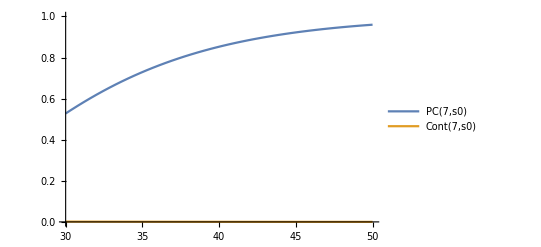

```mathematica
Plot[{PC[7,s0],Cont[7,s0]},{s0,30,50},PlotRange->{{30,50},{0,1}},PlotLegends->"Expressions"]
```

```mathematica
conv[M2_,s0_]:= BPiDim5[M2]/KRD[M2,s0]
```

```mathematica
conv[4,37]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {8.72139×10^-11}. NIntegrate obtained -9.92617×10^-24 and 9.19653×10^-22 for the integral and error estimates.

0.0001404

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {0.195297}. NIntegrate obtained 2.23339×10^-23 and 8.78512×10^-24 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {0.195297}. NIntegrate obtained -2.97268×10^-24 and 5.19626×10^-25 for the integral and error estimates.

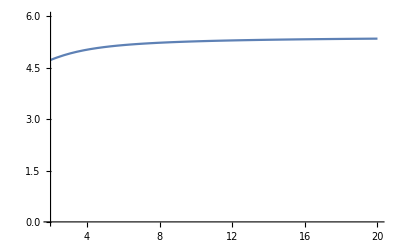

0.000429389

```mathematica
grM2=Plot[massB[M2,35],{M2,2,20},PlotRange->{{2,20},{0,6}}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {0.195297}. NIntegrate obtained -2.97268×10^-24 and 5.19626×10^-25 for the integral and error estimates.

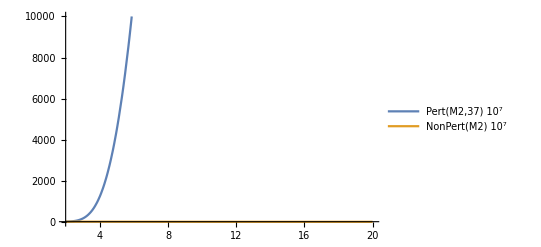

```mathematica
grPertNonPert=Plot[{Pert[M2,37]*10^7,NonPert[M2]*10^7},{M2,2,20},PlotRange->{{2,20},{-10,10000}},PlotLegends->"Expressions"]
```

```mathematica
(*GRAFİK*)
```

```mathematica
(*M2=6-9, s0=36-38*)
```

```mathematica
masss036=Export["masss036.dat",Table[{Msq,massB[Msq,36]},{Msq,6,9,0.1}]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {0.0742032}. NIntegrate obtained -3.97047×10^-21 and 2.31132×10^-21 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {0.0722501}. NIntegrate obtained -5.45939×10^-22 and 9.38429×10^-23 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {0.513656}. NIntegrate obtained -4.92338×10^-21 and 2.51579×10^-21 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

masss036.dat

```mathematica
masss037=Export["masss037.dat",Table[{Msq,massB[Msq,37]},{Msq,6,9,0.1}]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {0.0742032}. NIntegrate obtained -3.97047×10^-21 and 2.31132×10^-21 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {0.0722501}. NIntegrate obtained -5.45939×10^-22 and 9.38429×10^-23 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {0.513656}. NIntegrate obtained -4.92338×10^-21 and 2.51579×10^-21 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

masss037.dat

```mathematica
masss038=Export["masss038.dat",Table[{Msq,massB[Msq,38]},{Msq,6,9,0.1}]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {0.0742032}. NIntegrate obtained -3.97047×10^-21 and 2.31132×10^-21 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {0.0722501}. NIntegrate obtained -5.45939×10^-22 and 9.38429×10^-23 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {0.513656}. NIntegrate obtained -4.92338×10^-21 and 2.51579×10^-21 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

masss038.dat

```mathematica
masss036A=Import["masss036.dat", "Table"]
```

{{6.,5.19116},{6.1,5.19617},{6.2,5.20102},{6.3,5.20573},{6.4,5.21029},{6.5,5.21471},{6.6,5.219},{6.7,5.22316},{6.8,5.22721},{6.9,5.23113},{7.,5.23495},{7.1,5.23866},{7.2,5.24226},{7.3,5.24577},{7.4,5.24918},{7.5,5.25249},{7.6,5.25572},{7.7,5.25887},{7.8,5.26193},{7.9,5.26492},{8.,5.26782},{8.1,5.27066},{8.2,5.27342},{8.3,5.27612},{8.4,5.27875},{8.5,5.28132},{8.6,5.28382},{8.7,5.28627},{8.8,5.28866},{8.9,5.29099},{9.,5.29327}}

```mathematica
masss037A=Import["masss037.dat", "Table"]
```

{{6.,5.21679},{6.1,5.22228},{6.2,5.22761},{6.3,5.23278},{6.4,5.23779},{6.5,5.24266},{6.6,5.24738},{6.7,5.25196},{6.8,5.25641},{6.9,5.26074},{7.,5.26494},{7.1,5.26903},{7.2,5.27301},{7.3,5.27687},{7.4,5.28064},{7.5,5.2843},{7.6,5.28787},{7.7,5.29134},{7.8,5.29473},{7.9,5.29803},{8.,5.30124},{8.1,5.30438},{8.2,5.30744},{8.3,5.31042},{8.4,5.31333},{8.5,5.31617},{8.6,5.31895},{8.7,5.32165},{8.8,5.3243},{8.9,5.32689},{9.,5.32941}}

```mathematica
masss038A=Import["masss038.dat", "Table"]
```

{{6.,5.2403},{6.1,5.24629},{6.2,5.25209},{6.3,5.25773},{6.4,5.2632},{6.5,5.26851},{6.6,5.27367},{6.7,5.27868},{6.8,5.28354},{6.9,5.28828},{7.,5.29288},{7.1,5.29736},{7.2,5.30171},{7.3,5.30595},{7.4,5.31008},{7.5,5.31409},{7.6,5.31801},{7.7,5.32182},{7.8,5.32554},{7.9,5.32916},{8.,5.33269},{8.1,5.33613},{8.2,5.3395},{8.3,5.34277},{8.4,5.34598},{8.5,5.3491},{8.6,5.35215},{8.7,5.35513},{8.8,5.35805},{8.9,5.36089},{9.,5.36367}}

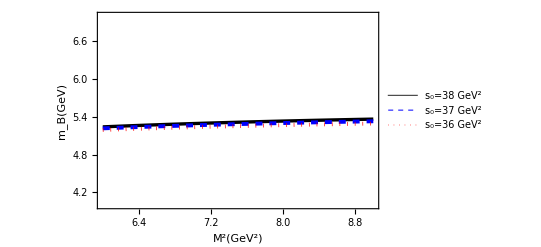

```mathematica
grmassMsq=ListLinePlot[{masss038A,masss037A,masss036A},PlotRange->{{6,9},{4,7}},(*PlotMarkers->{{●,10},{■,15}},*)PlotStyle->{{Thickness[0.006], Black},{Thickness[0.007],Blue,Dashed},{Thickness[0.007],Red, Dotted}},Frame->True,LabelStyle->Directive[Black,12],FrameLabel->{"M^2(GeV^2)","m_B(GeV)"},FrameStyle->Directive[Bold,14],PlotLegends->Placed[LineLegend[{"s_0=38 GeV^2","s_0=37 GeV^2","s_0=36 GeV^2"},LegendMarkerSize->{{70,10}},LabelStyle->{FontSize->12}],{0.5,0.75}]]
```

```mathematica
Export["MassBvsMsq.eps", grmassMsq,"EPS"]
```

MassBvsMsq.eps

```mathematica
(*s0 integrali*)
```

```mathematica
massM26=Export["massM26.dat",Table[{s0,massB[6,s0]},{s0,36,38,0.1}]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {0.0742032}. NIntegrate obtained -3.97047×10^-21 and 2.31132×10^-21 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {0.0722501}. NIntegrate obtained -5.45939×10^-22 and 9.38429×10^-23 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {0.0742032}. NIntegrate obtained -3.97047×10^-21 and 2.31132×10^-21 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

massM26.dat

```mathematica
massM275=Export["massM275.dat",Table[{s0,massB[7.5,s0]},{s0,36,38,0.1}]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {0.580063}. NIntegrate obtained -8.47033×10^-22 and 4.15706×10^-21 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {0.0820157}. NIntegrate obtained -7.74241×10^-22 and 2.17567×10^-22 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {0.580063}. NIntegrate obtained -8.47033×10^-22 and 4.15706×10^-21 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

massM275.dat

```mathematica
massM29=Export["massM29.dat",Table[{s0,massB[9,s0]},{s0,36,38,0.1}]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {1.79352×10^-8}. NIntegrate obtained -1.69407×10^-21 and 2.65904×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {1.79352×10^-8}. NIntegrate obtained -2.11758×10^-22 and 2.88309×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {1.79352×10^-8}. NIntegrate obtained -1.69407×10^-21 and 2.65904×10^-17 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

massM29.dat

```mathematica
massM26A=Import["massM26.dat", "Table"]
```

{{36.,5.19116},{36.1,5.19382},{36.2,5.19646},{36.3,5.19908},{36.4,5.20167},{36.5,5.20424},{36.6,5.2068},{36.7,5.20933},{36.8,5.21183},{36.9,5.21432},{37.,5.21679},{37.1,5.21923},{37.2,5.22165},{37.3,5.22406},{37.4,5.22644},{37.5,5.2288},{37.6,5.23114},{37.7,5.23346},{37.8,5.23576},{37.9,5.23804},{38.,5.2403}}

```mathematica
massM275A=Import["massM275.dat", "Table"]
```

{{36.,5.25249},{36.1,5.25577},{36.2,5.25902},{36.3,5.26225},{36.4,5.26546},{36.5,5.26866},{36.6,5.27183},{36.7,5.27497},{36.8,5.2781},{36.9,5.28121},{37.,5.2843},{37.1,5.28737},{37.2,5.29042},{37.3,5.29345},{37.4,5.29646},{37.5,5.29944},{37.6,5.30241},{37.7,5.30536},{37.8,5.30829},{37.9,5.3112},{38.,5.31409}}

```mathematica
massM29A=Import["massM29.dat", "Table"]
```

{{36.,5.29327},{36.1,5.29697},{36.2,5.30066},{36.3,5.30432},{36.4,5.30796},{36.5,5.31158},{36.6,5.31519},{36.7,5.31877},{36.8,5.32234},{36.9,5.32588},{37.,5.32941},{37.1,5.33292},{37.2,5.33641},{37.3,5.33989},{37.4,5.34334},{37.5,5.34677},{37.6,5.35019},{37.7,5.35359},{37.8,5.35697},{37.9,5.36033},{38.,5.36367}}

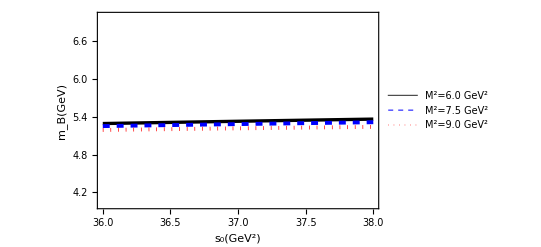

```mathematica
grmasss0=ListLinePlot[{massM29A,massM275A,massM26A},PlotRange->{{36,38},{4,7}},(*PlotMarkers->Automatic,*)PlotStyle->{{Thickness[0.006], Black},{Thickness[0.007],Blue,Dashed},{Thickness[0.007],Red, Dotted}},Frame->True,LabelStyle->Directive[Black,12],FrameLabel->{"s_0(GeV^2)","m_B(GeV)"},FrameStyle->Directive[Bold,14],PlotLegends->Placed[LineLegend[{"M^2=6.0 GeV^2","M^2=7.5 GeV^2","M^2=9.0 GeV^2"},LegendMarkerSize->{{70,10}},LabelStyle->{FontSize->12}],{0.5,0.75}]]
```

```mathematica
Export["MassBvss0.eps", grmasss0,"EPS"]
```

MassBvss0.eps

```mathematica
(**f grafik*)
```

```mathematica
masss036=Export["masss036.dat",Table[{Msq,massB[Msq,36]},{Msq,6,9,0.1}]]
```